SimulationTools > Simulation Information

# Simulation Information

SimulationTools provides functions for accessing information about a simulation. This currently works best with Cactus simulations. For full functionality, certain output must have been enabled for the simulation. See the Supported Codes and Data Formats tutorial for more information.

## Getting an overview of a simulation

SimulationOverview

Simulation overview.

SimulationOverview can be used for a quick, at a glance overview of the status of a simulation, including the run speed, memory usage, trajectories, waveforms and run time. Its current focus is on binary black hole simulations using Cactus, but it has an extensible interface which will allow it to support other simulation types in the future.

```mathematica
$SimulationPath={$SimulationToolsTestSimulationDirectory};
```

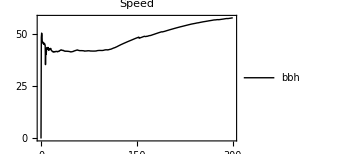
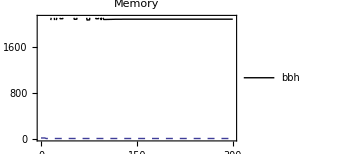
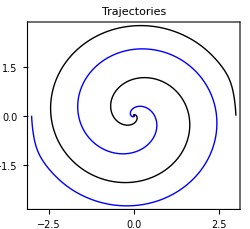
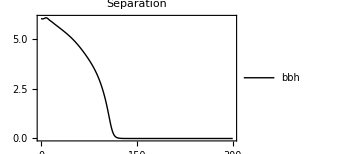
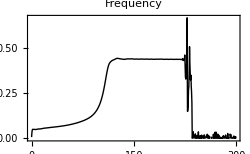
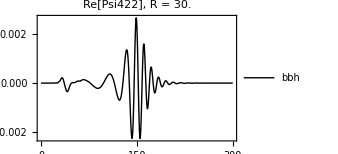
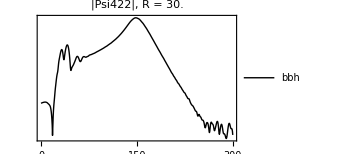
bbh | 
-Graphics- | -Graphics-
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-
Simulation | Cores | CPU hrs. | Days | CPU hrs./day | Estimated finish
bbh | 12 | 62.5898 | 0.217326 | 288 | Finished | 
Simulation | Segments
bbh | Segment | Last output | t1 | t2
0000 | Fri 30 Mar 2012 14:24:13 | 0 | 6.5
0001 | Fri 30 Mar 2012 14:24:16 | 7 | 300 |

```mathematica
SimulationOverview["bbh"]
```

## Accessing individual simulation statistics

ReadSimulationRunTime | ReadSimulationSpeed
ReadSimulationCost | ReadSimulationCoreCount

Accessing statistics on a simulation.

We can compute the total number of hours the simulation has run for,

```mathematica
ReadSimulationRunTime[$SimulationToolsTestSimulation]/3600
```

5.21581

the speed of the evolution (evolved coordinate time per hour as a function of the simulation coordinate time)

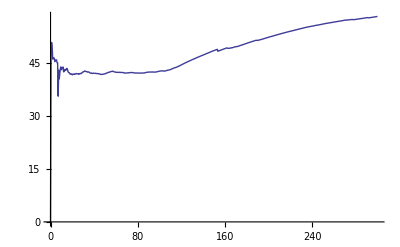

```mathematica
ListLinePlot[ReadSimulationSpeed[$SimulationToolsTestSimulation]]
```

memory usage

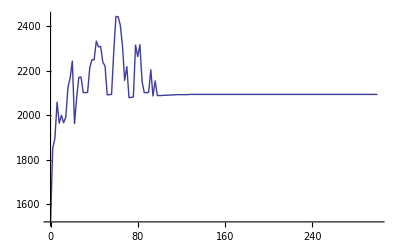

```mathematica
ListLinePlot[ReadSimulationMemoryUsage[$SimulationToolsTestSimulation],PlotRange->All]
```

swap usage

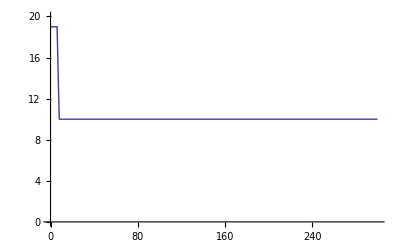

```mathematica
ListLinePlot[ReadSimulationSwapUsage[$SimulationToolsTestSimulation]]
```

the number of CPU cores used

```mathematica
ReadSimulationCoreCount[$SimulationToolsTestSimulation]
```

12

and the total computational cost of the simulation in CPU hours

```mathematica
ReadSimulationCost[$SimulationToolsTestSimulation]
```

62.5898

Much of this information is available only if the simulation was run using SimFactory.  Support for alternative systems can be added as required.

SupportedCodesAndDataFormats

Parameters